```mathematica
(*Universal*)
G:= 6.6743 10^-11(*m^3 kg^-1 s^-2*)
eV := 1.6 10^-19 (* kg m^2 s^-2*)
Subscript[ρ, 0] := 0.4 10^9 1.6 10^-19 10^6 (* kg m^-1 s^-2*)
Subscript[σ, v] := 160000 (*m/s*)
hbar :=1.05457182 10^-34(* kg m^2 s^-1*)
c := 3 10^8 (* m/s *)
MassScale:=c^2*hbar/eV

(*BM1 & BM2*)
T :=10 365  24 60  60  (*s*)
Subscript[Δt, 2] :=15 60 (*s*)
Δt := 4  7  24  60  60 (*s*)
Subscript[N, star]:= 10^8 (*number*)
Subscript[N, star2] := 10^7
Subscript[σ, r] := 100  10^-6 * Pi/206264.5 (*rad*)
```

```mathematica
(*Check*)
Pi
MassScale
Subscript[ρ, 0]
Subscript[N, star2]
```

## Full Sensitivity curve of the BM1 and BM2

1.97238×10^31

1

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

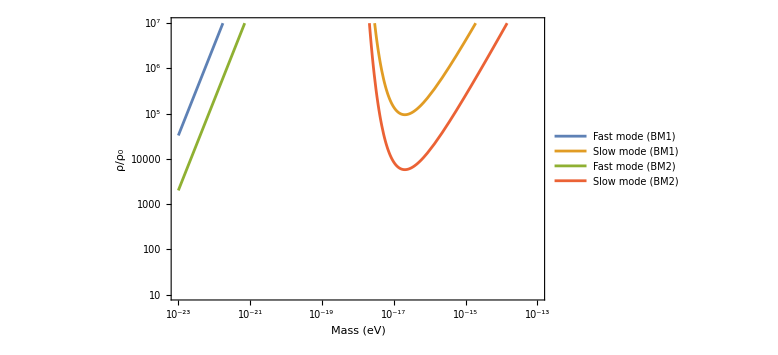

```mathematica
RelativeNorm := (hbar*c^8)/(8 √2*Pi^3)
RelativeNorm
OveralNorm := 1
OveralNorm

T :=10 365  24 60  60  (*s*)


Subscript[S, slow][f_, m_] :=1/(m^3 f^2)*(8 G^2)/Subscript[σ, v]^4 BesselK[0,Abs[ (2 π f)/(m Subscript[σ, v]^2)]]
Subscript[SNR, slow][m_]:=((4T*hbar^3)/(27 (Δt)^2) * Subscript[N, star]^2/Subscript[σ, r]^4* NIntegrate[(Subscript[S, slow][f, m])^2, {f, 1/T, 1/(2 Δt)}, MinRecursion->9])^(1/4)

Subscript[S, fast][m_] := (3π)/2(G^2 Subscript[σ, v]^2)/m^4 
Subscript[SNR, fast][m_]:=((4T*hbar^3)/(27 (Δt)^2) * Subscript[N, star]^2/Subscript[σ, r]^4*(Subscript[S, fast][m])^2)^(1/4)


Subscript[S, slow2][f_, m_] :=1/(m^3 f^2)*(8 G^2)/Subscript[σ, v]^4 BesselK[0,Abs[ (2 π f)/(m Subscript[σ, v]^2)]]
Subscript[SNR, slow2][m_]:=((4T*hbar^3)/(27 (Subscript[Δt, 2])^2) * Subscript[N, star2]^2/Subscript[σ, r]^4* NIntegrate[(Subscript[S, slow2][f, m])^2, {f, 1/T, 1/(2 Subscript[Δt, 2])}, MinRecursion->9])^(1/4)

Subscript[S, fast2][m_] := (3π)/2(G^2 Subscript[σ, v]^2)/m^4 
Subscript[SNR, fast2][m_]:=((4T*hbar^3)/(27 (Subscript[Δt, 2])^2) * Subscript[N, star2]^2/Subscript[σ, r]^4*(Subscript[S, fast2][m])^2)^(1/4)


LogLogPlot[{(RelativeNorm*OveralNorm)/(Subscript[SNR, fast][m/MassScale]*Subscript[ρ, 0]),OveralNorm/(Subscript[SNR, slow][m/MassScale]*Subscript[ρ, 0]), (RelativeNorm*OveralNorm)/(Subscript[SNR, fast2][m/MassScale]*Subscript[ρ, 0]),OveralNorm/(Subscript[SNR, slow2][m/MassScale]*Subscript[ρ, 0])} , {m, 10^-23, 10^-13}, PlotRange->{{10^-23, 10^-13},{10^1,10^7}},
Frame->True,ImageSize->Large,
FrameLabel->{Style["Mass (eV)",12,Bold],Style["ρ/ρ_0",20,Bold]},
TicksStyle->Directive[FontSize->10],LabelStyle->Directive[FontSize->10],
PlotLegends->Placed[LineLegend[{"Fast mode (BM1)", "Slow mode (BM1)", "Fast mode (BM2)", "Slow mode (BM2)"}],{Right,Bottom}]]
```

## (Obsolute) Full curve of the fast mode

General::munfl: (1.00094×10^-100)^4 is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

General::munfl: (2.56196×10^-100)^4 is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

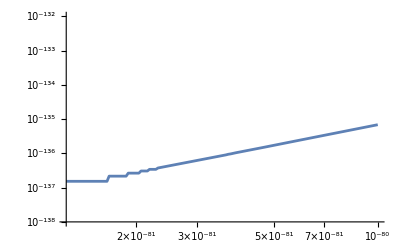

```mathematica
(* Is there minimum at the fast mode?*)
LogLogPlot[{RelativeNorm/(Subscript[SNR, fast][m]),1/(Subscript[SNR, slow][m])} , {m, 10^-100, 10^-80}, PlotRange->{10^-138,10^-132}]
```

## Can we improve sensitivity by increasing T?

1.97238×10^31

1

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

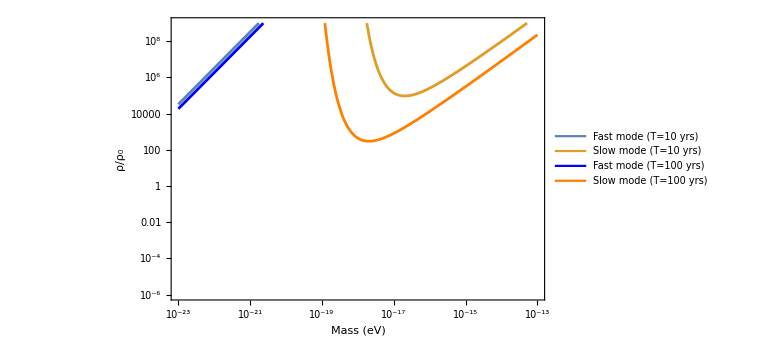

```mathematica
RelativeNorm := (hbar*c^8)/(8 √2*Pi^3)
RelativeNorm
OveralNorm := 1
OveralNorm

T :=10 365  24 60  60  (*s*)
Subscript[S, slow][f_, m_] :=1/(m^3 f^2)*(8 G^2)/Subscript[σ, v]^4 BesselK[0,Abs[ (2 π f)/(m Subscript[σ, v]^2)]]
Subscript[SNR, slow][m_]:=((4T*hbar^3)/(27 (Δt)^2) * Subscript[N, star]^2/Subscript[σ, r]^4* NIntegrate[(Subscript[S, slow][f, m])^2, {f, 1/T, 1/(2 Δt)}, MinRecursion->9])^(1/4)

Subscript[S, fast][m_] := (3π)/2(G^2 Subscript[σ, v]^2)/m^4 
Subscript[SNR, fast][m_]:=((4T*hbar^3)/(27 (Δt)^2) * Subscript[N, star]^2/Subscript[σ, r]^4*(Subscript[S, fast][m])^2)^(1/4)



TT :=100 365  24 60  60  (*s*)
Subscript[S, slowT][f_, m_] :=1/(m^3 f^2)*(8 G^2)/Subscript[σ, v]^4 BesselK[0,Abs[ (2 π f)/(m Subscript[σ, v]^2)]]
Subscript[SNR, slowT][m_]:=((4TT*hbar^3)/(27 (Δt)^2) * Subscript[N, star]^2/Subscript[σ, r]^4* NIntegrate[(Subscript[S, slowT][f, m])^2, {f, 1/TT, 1/(2 Δt)}, MinRecursion->9])^(1/4)

Subscript[S, fastT][m_] := (3π)/2(G^2 Subscript[σ, v]^2)/m^4 
Subscript[SNR, fastT][m_]:=((4TT*hbar^3)/(27 (Δt)^2) * Subscript[N, star]^2/Subscript[σ, r]^4*(Subscript[S, fastT][m])^2)^(1/4)


LogLogPlot[{(RelativeNorm*OveralNorm)/(Subscript[SNR, fast][m/MassScale]*Subscript[ρ, 0]),OveralNorm/(Subscript[SNR, slow][m/MassScale]*Subscript[ρ, 0]), (RelativeNorm*OveralNorm)/(Subscript[SNR, fastT][m/MassScale]*Subscript[ρ, 0]),OveralNorm/(Subscript[SNR, slowT][m/MassScale]*Subscript[ρ, 0])} , {m, 10^-23, 10^-13}, PlotRange->{{10^-23, 10^-13},{10^-6,10^9}},
Frame->True,ImageSize->Large,
FrameLabel->{Style["Mass (eV)",12,Bold],Style["ρ/ρ_0",20,Bold]},
TicksStyle->Directive[FontSize->10],LabelStyle->Directive[FontSize->10],
PlotStyle->{RGBColor[0.368417,0.506779,0.709798], RGBColor[0.880722,0.611041,0.142051], Blue, Orange},
PlotLegends->Placed[LineLegend[{RGBColor[0.368417,0.506779,0.709798], RGBColor[0.880722,0.611041,0.142051], Blue, Orange},{"Fast mode (T=10 yrs)", "Slow mode (T=10 yrs)", "Fast mode (T=100 yrs)", "Slow mode (T=100 yrs)"}],{Right,Bottom}]]
```

## Full fast mode curve with large T

1.97238×10^31

1

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

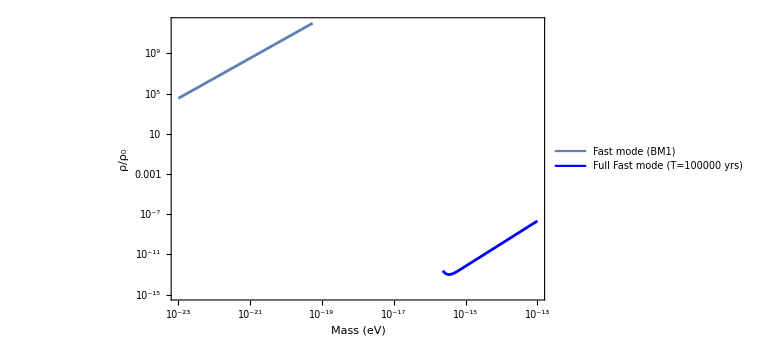

```mathematica
RelativeNorm := (hbar*c^8)/(8 √2*Pi^3)
RelativeNorm
OveralNorm := 1
OveralNorm


TT :=100000 365  24 60  60  (*s*)

Subscript[S, fast][m_] := (3π)/2(G^2 Subscript[σ, v]^2)/m^4 
Subscript[SNR, fast][m_]:=((4T*hbar^3)/(27 (Δt)^2) * Subscript[N, star]^2/Subscript[σ, r]^4*(Subscript[S, fast][m])^2)^(1/4)

Subscript[S, fastFULL][f_, m_] := π^3/2 G^2/(m^5 Subscript[σ, v]^6)(2π f/m-2)^6 Exp[- (2π f/m-2)^2/Subscript[σ, v]^2]
Subscript[SNR, fastFULL][m_]:=((4TT*hbar^3)/(27 (Δt)^2) * Subscript[N, star]^2/Subscript[σ, r]^4* NIntegrate[(Subscript[S, fastFULL][f, m])^2, {f, 1/TT, 1/(2 Δt)}, MaxRecursion->12, MinRecursion->12])^(1/4)




LogLogPlot[{(RelativeNorm*OveralNorm)/(Subscript[SNR, fast][m/MassScale]*Subscript[ρ, 0]),OveralNorm/(Subscript[SNR, fastFULL][m/MassScale]*Subscript[ρ, 0])} , {m, 10^-23, 10^-13}, PlotRange->{{10^-23, 10^-13},{10^-15,10^12}},
Frame->True,ImageSize->Large,
FrameLabel->{Style["Mass (eV)",12,Bold],Style["ρ/ρ_0",20,Bold]},
TicksStyle->Directive[FontSize->10],LabelStyle->Directive[FontSize->10],
PlotStyle->{RGBColor[0.368417,0.506779,0.709798],Blue},
PlotLegends->Placed[LineLegend[{RGBColor[0.368417,0.506779,0.709798], Blue},
{"Fast mode (BM1)",  "Full Fast mode (T=100000 yrs)"}],{Left,Bottom}]]
```

## (Obsolute) Mid-presentation code

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

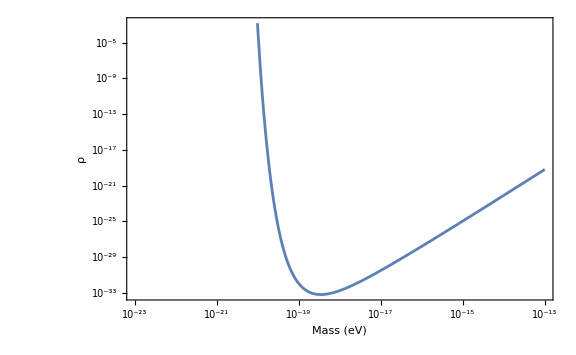

```mathematica
(*Subscript[S, slow][f_, m_] :=1/(m^3 f^2)*(8 G^2)/Subscript[σ, v]^4 BesselK[0,Abs[ (2 π f)/(m Subscript[σ, v]^2)]]
Subscript[SNR, slow][m_]:=((4T)/(27 (Δt)^2) * Subscript[N, star]^2/Subscript[σ, r]^4* NIntegrate[(Subscript[S, slow][f, m])^2, {f, 1/T, 1/(2 Δt)}])^(1/2)

(*f[m_]:=Subscript[SNR, slow][m/(1.6 10^-19)];
LogLogPlot[f[m]/Subscript[ρ, 0], {m, 0, 1}]*)

LogLogPlot[1/(Subscript[SNR, slow][m]* Subscript[ρ, 0]), {m, 10^-23, 10^-13},
Frame->True,ImageSize->Large,
FrameLabel->{Style["Mass (eV)",32,Bold],Style["ρ",40,Bold]},
TicksStyle->Directive[FontSize->20],LabelStyle->Directive[FontSize->20]
]*)
```

6.54518×10^101

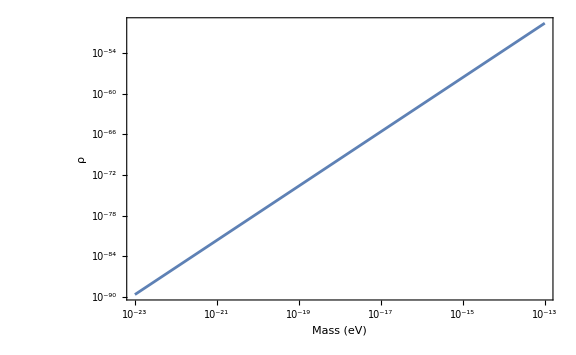

```mathematica
(*

Subscript[S, fast][m_] := (3π)/2(G^2 Subscript[σ, v]^2)/m^4 
Subscript[SNR, fast][m_]:=((4T)/(27 (Δt)^2) * Subscript[N, star]^2/Subscript[σ, r]^4*(Subscript[S, fast][m])^2)^(1/2)
Subscript[SNR, fast][10^-22]
LogLogPlot[1/(Subscript[SNR, fast][m]* Subscript[ρ, 0]), {m, 10^-23, 10^-13},
Frame->True,ImageSize->Large,
FrameLabel->{Style["Mass (eV)",32,Bold],Style["ρ",40,Bold]},
TicksStyle->Directive[FontSize->20],LabelStyle->Directive[FontSize->20]
]*)
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

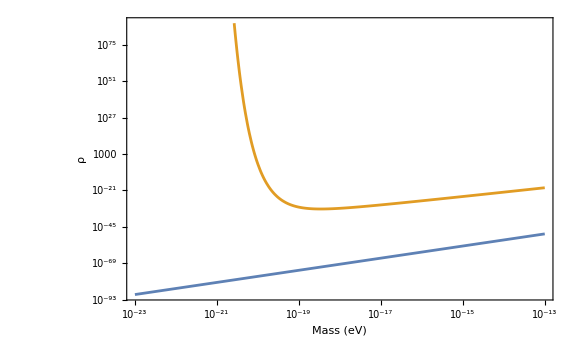

```mathematica
(*LogLogPlot[{1/(Subscript[SNR, fast][m]* Subscript[ρ, 0]),1/(Subscript[SNR, slow][m]* Subscript[ρ, 0])} , {m, 10^-23, 10^-13}, 
Frame->True,ImageSize->Large,
FrameLabel->{Style["Mass (eV)",32,Bold],Style["ρ",40,Bold]},
TicksStyle->Directive[FontSize->20],LabelStyle->Directive[FontSize->20]]*)
```

## Comparison with other group’s paper

1.97238×10^31

1

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

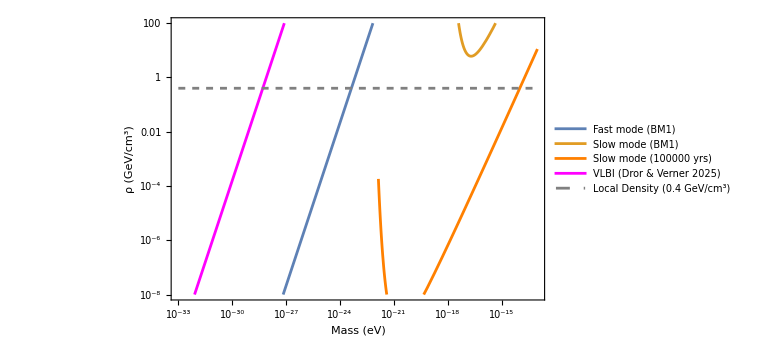

```mathematica
RelativeNorm := (hbar*c^8)/(8 √2*Pi^3)
RelativeNorm
OveralNorm := 1
OveralNorm

T :=10 365  24 60  60  (*s*)


Subscript[S, slow][f_, m_] :=1/(m^3 f^2)*(8 G^2)/Subscript[σ, v]^4 BesselK[0,Abs[ (2 π f)/(m Subscript[σ, v]^2)]]
Subscript[SNR, slow][m_]:=((4T*hbar^3)/(27 (Δt)^2) * Subscript[N, star]^2/Subscript[σ, r]^4* NIntegrate[(Subscript[S, slow][f, m])^2, {f, 1/T, 1/(2 Δt)}, MinRecursion->9])^(1/4)

Subscript[S, fast][m_] := (3π)/2(G^2 Subscript[σ, v]^2)/m^4 
Subscript[SNR, fast][m_]:=((4T*hbar^3)/(27 (Δt)^2) * Subscript[N, star]^2/Subscript[σ, r]^4*(Subscript[S, fast][m])^2)^(1/4)




TT :=100000 365  24 60  60  (*s*)
Subscript[S, slowT][f_, m_] :=1/(m^3 f^2)*(8 G^2)/Subscript[σ, v]^4 BesselK[0,Abs[ (2 π f)/(m Subscript[σ, v]^2)]]
Subscript[SNR, slowT][m_]:=((4TT*hbar^3)/(27 (Δt)^2) * Subscript[N, star]^2/Subscript[σ, r]^4* NIntegrate[(Subscript[S, slowT][f, m])^2, {f, 1/TT, 1/(2 Δt)}, MinRecursion->9])^(1/4)




LogLogPlot[{(RelativeNorm*OveralNorm)/(Subscript[SNR, fast][m/MassScale]),OveralNorm/(Subscript[SNR, slow][m/MassScale]),OveralNorm/(Subscript[SNR, slowT][m/MassScale]), 10^58/64 m^2,  0.4} , {m, 10^-33, 10^-13}, PlotRange->{{10^-33, 10^-13},{10^-8,10^2}},
Frame->True,ImageSize->Large,
FrameLabel->{Style["Mass (eV)",12,Bold],Style["ρ (GeV/cm^3)",20,Bold]},FrameTicks->Automatic,
TicksStyle->Directive[FontSize->10],LabelStyle->Directive[FontSize->10],
PlotStyle->{RGBColor[0.368417,0.506779,0.709798], RGBColor[0.880722,0.611041,0.142051],Orange, Magenta, {Gray, Dashed}},
PlotLegends->Placed[LineLegend[{"Fast mode (BM1)", "Slow mode (BM1)","Slow mode (100000 yrs)", "VLBI (Dror & Verner 2025)", "Local Density (0.4 GeV/cm^3)"}],{Right,Bottom}]]
```